```mathematica
SphericalToCartesian[{r_, θ_, ϕ_}]:={
r * Sin[θ] * Cos[ϕ],
r * Sin[θ] * Sin[ϕ], 
r * Cos[θ]
};
CartesianToSpherical=Function[xyz,
If[xyz[[1]]==0&&xyz[[2]]==0,
{Abs[xyz[[3]]],0,If[xyz[[3]]≥0,0,Pi]},
CoordinateTransform["Cartesian"->"Spherical",xyz]
]
];
```

```mathematica
sphericalCoordinates = Flatten[Table[
{Cos[x*Pi/180/2],x*Pi/180,y*Pi/180},
{y,-90,90,15},
{x,-180,180,15}
], 1];
M = RotationTransform[45*Pi/180, {1,0,0}];
cartesianCoordinates =SphericalToCartesian/@sphericalCoordinates;
cartesianCoordinates = M/@cartesianCoordinates;
points = Point/@cartesianCoordinates;
display = Flatten[{
Sphere[{0, 0, 0}, 0.0],
Blue,Line[{{-1.5,0,0},{1.5,0,0}}],
Green,Line[{{0,-1.5,0},{0,1.5,0}}],
Red,Line[{{0,0,-1.5},{0,0,1.5}}],
Black,points
}, 1];
Graphics3D[display, Axes->True,AxesStyle->{Blue,Green,Red}, RotationAction->"Clip", Boxed->False]
```

-Graphics3D-

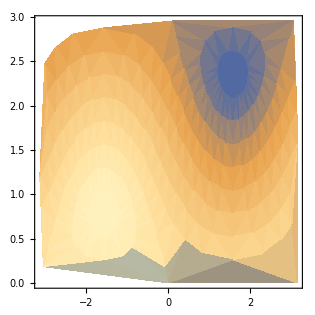

-Graphics3D-

```mathematica
rotatedSphericalCoordinates=({#[[3]],#[[2]],#[[1]]})&/@(CartesianToSpherical/@cartesianCoordinates);
ListDensityPlot[rotatedSphericalCoordinates]
ListPointPlot3D[rotatedSphericalCoordinates]
```